## ChatGPT 内部

```mathematica
GPTNet=NetModel["GPT2 Transformer Trained on WebText Data"]
```

NetChain[<2>]

## 嵌入向量

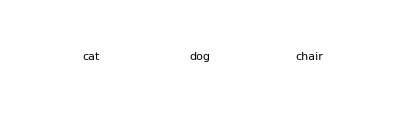

```mathematica
Labeled[ArrayPlot[Partition[
First[NetExtract[GPTNet,{"embedding","embeddingtokens"}][NetExtract[GPTNet,"Input"][#]]],32],Frame->None,ImageSize->150,ColorFunction->{{"[◼]", "ChatTechColors"}}["Orange"]],#]&/@{"cat","dog","chair"}//GraphicsRow
```

## 注意力块

```mathematica
Information[NetFlatten@NetExtract[GPTNet,{"decoder",1}],"FullSummaryGraphic"]
```

-Graphics-

```mathematica
GraphicsRow[Table[MatrixPlot[
MovingAverage[MovingAverage[#,64]&/@Normal@NetExtract[GPTNet,{"decoder",n,"1","attention",1(*key*),"Net","Weights"}],64],Frame->False],{n,4}]]
```

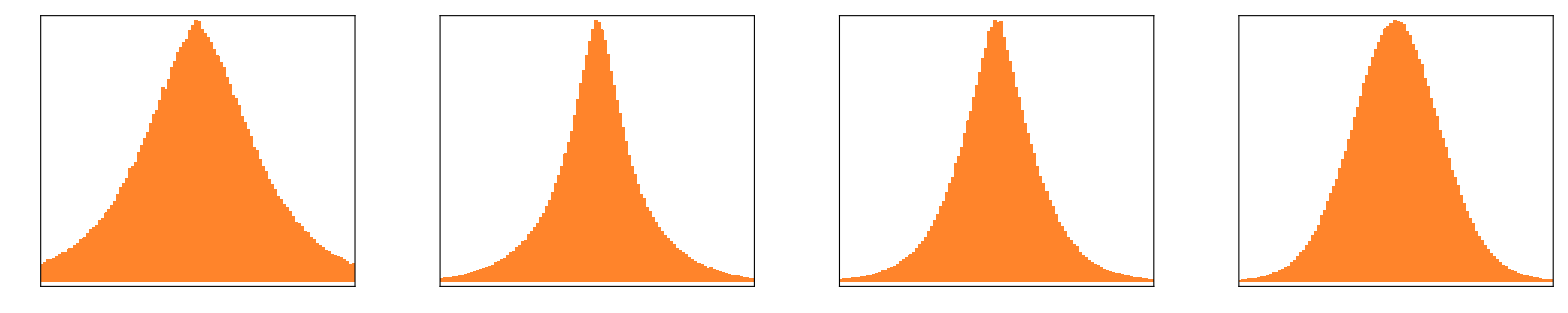

```mathematica
GraphicsRow[Table[Histogram[
Flatten@Normal@NetExtract[
GPTNet,{"decoder",n,"1","attention","1","Net","Weights"}],{.01},Frame->True,FrameTicks->None,PlotRange->{{-.5,.5},Automatic},ChartStyle->{{"[◼]", "ChatTechColors"}}["Data"]["Orange"]],{n,4}]]
```

## “语言法则”

## 文本结构

```mathematica
TextStructure["The best thing about AI is its ability to learn from experience.","ConstituentGraphs"]//First
```

-Graphics-

## “运动语义定律”

```mathematica
Module[{promptcolor, color,tokens,promptlength,
promptsteps,steps,continuation0,features2D0},
tokens=;
promptlength=9;
promptsteps=Range[promptlength];
steps=Range[promptlength,12];
continuation0=;
features2D0=DimensionReduce[NetModel["GPT2 Transformer Trained on WebText Data"]@continuation0,2,Method->"PrincipalComponentsAnalysis"];
promptcolor={{"[◼]", "ChatTechColors"}}["Normal"][.2]; color=RGBColor[{15, 162, 127}/255];
ListPlot[{Part[Thread[features2D0->FoldList[StringJoin,tokens]],promptsteps],
Part[Thread[features2D0->FoldList[StringJoin,tokens]],steps]},LabelingFunction->Callout,ImageSize->550,PlotStyle->{promptcolor,color},Prolog->{{Arrowheads[.03],{promptcolor,Thick,Line[features2D0[[promptsteps]]]},{color,Thick,Arrow[features2D0[[steps]]]}}},Frame->True,FrameTicks->None,Axes->False]]
```

-Graphics-

```mathematica
With[{resultsGPT2=},
Graphics3D[{{AbsoluteThickness[2],{{"[◼]", "ChatTechColors"}}["Normal"][0.2],
Line[MapIndexed[Append[#1,First[#2]]&,resultsGPT2⟦"PromptPoints"⟧]]},Table[{{Black,
Table[{AbsoluteThickness[2],Opacity[resultsGPT2⟦"Probabilities",i,j⟧+0.03],Line[{Append[resultsGPT2⟦"Points",i-1,-1⟧,i-1],Append[resultsGPT2⟦"Points",i,j⟧,i]}]},{j,resultsGPT2["Continuations"]-1}]},{RGBColor[1/255 {15,162,127}],AbsoluteThickness[2],Line[{Append[resultsGPT2⟦"Points",i-1,-1⟧,i-1],Append[resultsGPT2⟦"Points",i,-1⟧,i]}]}},{i,resultsGPT2["PromptLength"]+1,resultsGPT2["PromptLength"]+resultsGPT2["ContinuationLength"]}]},BoxRatios->{1,1,GoldenRatio},ViewPoint->{-1.5,-3,2},ViewVertical->{-1,0,0}]]
```

-Graphics3D-